## Legend for coloring

Flow of the discussion and labels for the action being performed.

Technical comments (mostly on the Mathematica commands).

Comments and thoughts on what we are seeing.

## Technical Setup

This function is used to manually specify the bins in the histograms so that I can separate the distances that are exactly 0.0 from the ones that are close to 0. The automatic bin generation lumps those together.
To do this, I feed in a list of pairs of x-coordinates representing each particular bin I want the histogram command to use. The first of those pairs goes from a negative number to a very small number close to 0. The rest is just generated with the table command.

```mathematica
bins[dx_,max_]:={Join[{-dx,0.000001},Table[i,{i,dx,max,dx}]]}
```

Define some system-specific variables here - e.g. the base path for where the data files are stored. For some reason, Mathematica does not import the file successfully if it’s just located in the same folder and the path is omitted.

```mathematica
pathBase="/Users/ivanevtimov/GDrive-Laf/THESIS/Results with more subjects/";
```

This will save time in replicating the results across subjects.

```mathematica
euclideanHistogram[filename_,maxval_]:=(
Clear[dataCurrSubj];
dataCurrSubj=Import[filename,Path->pathBase,HeaderLines->1];
Histogram[{dataCurrSubj[[All,3]],dataCurrSubj[[All,4]],dataCurrSubj[[All,5]],dataCurrSubj[[All,9]],dataCurrSubj[[All,10]],dataCurrSubj[[All,11]]},bins[10,maxval],ChartLegends->{"Fa Genuine","Fb Genuine","Rc Genuine", "Fa Imposter","Fb Imposter","Rc Imposter"},ChartStyle->{LightGray,LightBlue,Blue, Orange,LightRed,Red},AxesLabel->{"Euclidean distance from an fa-generated code", "Number of images"}])
```

```mathematica
hammingHistogram[filename_,maxval_]:=(
Clear[dataCurrSubj];
dataCurrSubj=Import[filename,Path->pathBase,HeaderLines->1];
Histogram[{dataCurrSubj[[All,6]],dataCurrSubj[[All,7]],dataCurrSubj[[All,8]],dataCurrSubj[[All,12]],dataCurrSubj[[All,13]],dataCurrSubj[[All,14]]},bins[0.2,maxval],ChartLegends->{"Fa Genuine","Fb Genuine","Rc Genuine", "Fa Imposter","Fb Imposter","Rc Imposter"},ChartStyle->{LightGray,LightBlue,Blue, Orange,LightRed,Red},AxesLabel->{"Hamming"}])
```

```mathematica
euclideanHistogramOnlyFAs[filename_,maxval_]:=(
Clear[dataCurrSubj];
dataCurrSubj=Import[filename,Path->pathBase,HeaderLines->1];
Histogram[{dataCurrSubj[[All,3]],dataCurrSubj[[All,9]]},bins[0.2,maxval],ChartLegends->{"Fa Genuine","Fb Genuine","Rc Genuine", "Fa Imposter","Fb Imposter","Rc Imposter"},ChartStyle->{LightGray, Orange},AxesLabel->{"Euclidean"}]);
hammingHistogramOnlyFAs[filename_,maxval_]:=(
Clear[dataCurrSubj];
dataCurrSubj=Import[filename,Path->pathBase,HeaderLines->1];
Histogram[{dataCurrSubj[[All,6]],dataCurrSubj[[All,12]]},bins[0.2,maxval],ChartLegends->{"Fa Genuine","Fb Genuine","Rc Genuine", "Fa Imposter","Fb Imposter","Rc Imposter"},ChartStyle->{LightGray, Orange},AxesLabel->{"Hamming"}]);
euclideanHistogramOnlyFBs[filename_,maxval_]:=(
Clear[dataCurrSubj];
dataCurrSubj=Import[filename,Path->pathBase,HeaderLines->1];
Histogram[{dataCurrSubj[[All,4]],dataCurrSubj[[All,10]]},bins[0.2,maxval],ChartLegends->{"Fa Genuine","Fb Genuine","Rc Genuine", "Fa Imposter","Fb Imposter","Rc Imposter"},ChartStyle->{LightBlue,LightRed},AxesLabel->{"Euclidean"}]);
hammingHistogramOnlyFBs[filename_,maxval_]:=(
Clear[dataCurrSubj];
dataCurrSubj=Import[filename,Path->pathBase,HeaderLines->1];
Histogram[{dataCurrSubj[[All,7]],dataCurrSubj[[All,13]]},bins[0.2,maxval],ChartLegends->{"Fa Genuine","Fb Genuine","Rc Genuine", "Fa Imposter","Fb Imposter","Rc Imposter"},ChartStyle->{LightBlue,LightRed},AxesLabel->{"Hamming"}]);
euclideanHistogramOnlyRCs[filename_,maxval_]:=(
Clear[dataCurrSubj];
dataCurrSubj=Import[filename,Path->pathBase,HeaderLines->1];
Histogram[{dataCurrSubj[[All,5]],dataCurrSubj[[All,11]]},bins[0.2,maxval],ChartLegends->{"Fa Genuine","Fb Genuine","Rc Genuine", "Fa Imposter","Fb Imposter","Rc Imposter"},ChartStyle->{Blue, Red},AxesLabel->{"Euclidean"}]);
hammingHistogramOnlyRCs[filename_,maxval_]:=(
Clear[dataCurrSubj];
dataCurrSubj=Import[filename,Path->pathBase,HeaderLines->1];
Histogram[{dataCurrSubj[[All,8]],dataCurrSubj[[All,14]]},bins[0.2,maxval],ChartLegends->{"Fa Genuine","Fb Genuine","Rc Genuine", "Fa Imposter","Fb Imposter","Rc Imposter"},ChartStyle->{Blue,Red},AxesLabel->{"Hamming"}]);
```

## Subject 00070 (Low FB and Low RC Matching Scores)

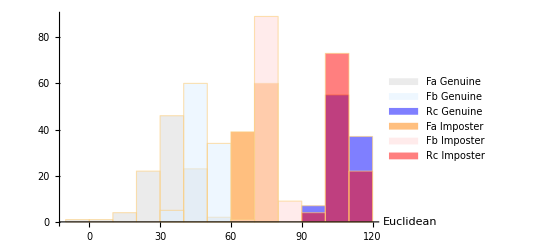

```mathematica
euclideanHistogram["data_howfar_vgg_subject_00070_with_imposter.csv",120]
```

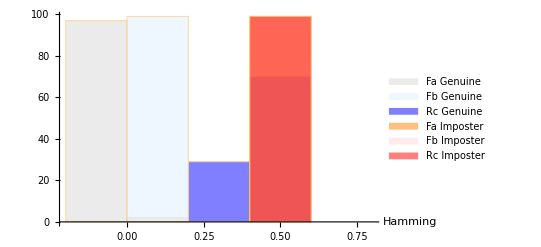

```mathematica
hammingHistogram["data_howfar_meb_subject_00070_with_imposter_.csv",0.8]
```

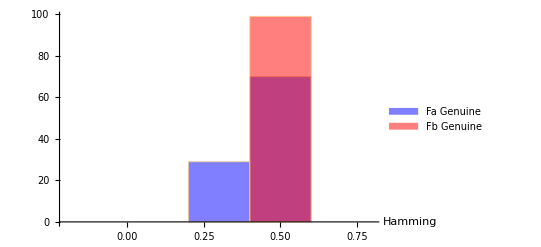

```mathematica
hammingHistogramOnlyRCs["data_howfar_meb_subject_00070_with_imposter_.csv",0.8]
```

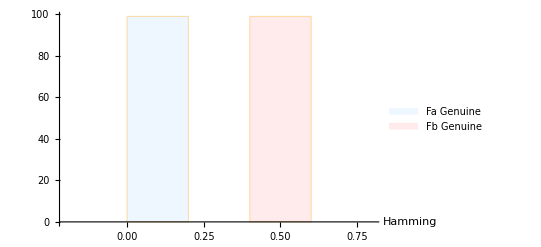

```mathematica
hammingHistogramOnlyFBs["data_howfar_meb_subject_00070_with_imposter_.csv",0.8]
```

## Subject 00140 (Good FB but Low RC Matching Scores)

## Subject 00468 (Almost Perfect FB but Low RC Matching Scores)

## Subject 00636 (Almost Perfect FB but Middle RC Matching Scores)

## Subject 00682 (Low FB, Low RC)